## Lesson 26: convolution integral

## Overview

You might expect that the product of LaplaceTransform is the transform of the product, but this is usually not the case:

```mathematica
LaplaceTransform[DiracDelta[t-1]Sin[t],t,s]==LaplaceTransform[DiracDelta[t-1],t,s]LaplaceTransform[Sin[t],t,s]
```

ⅇ^-s Sin[1]==ⅇ^-s/(1+s^2)

For this reason, mathematicians have developed a different operation known as convolution that shares many of the properties of multiplication and also commutes with LaplaceTransform:

```mathematica
LaplaceTransform[Integrate[f[t-r]g[r],{r,0,t}],t,s]
```

LaplaceTransform[f[t],t,s] LaplaceTransform[g[t],t,s]

The transform of the convolution is the product of the transform:

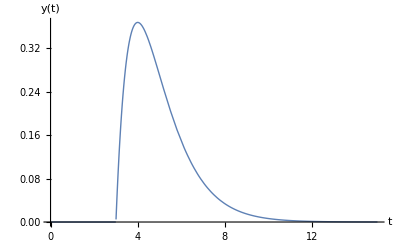

```mathematica
sln=Integrate[Exp[-(t-r)]*(t-r)DiracDelta[r-3],{r,0,t},Assumptions->t∈Reals];
Plot[sln,{t,0,15},]
```

## Convolution

The convolution of two functions is defined to be:

(f⊗g)(t)=∫_0^t f(t-r)g(r)ⅆr

You can define this operation using the following command:

```mathematica
Convolution[f_,g_]:=Integrate[f[t-r]g[r],{r,0,t},Assumptions->t>0]
```

It can be seen that convolution is commutative:

f⊗g=g⊗f

Convolution is also distributive:

f⊗(g+h)=f⊗g+f⊗h

And associative:

f⊗(g⊗h)=(f⊗g)⊗h

## Convolution Theorem

The convolution theorem states that:

L{(f⊗g)(t)}=L{f(t)}L{g(t)}

The transform of the convolution is thus the product of the transform.

For example, let

f(t)=sin(t)

g(t)=e^-t

Then their convolution can be calculated as:

```mathematica
conv=Integrate[Sin[t-r] Exp[-r],{r,0,t}]
```

1/2 (ⅇ^-t-Cos[t]+Sin[t])

And the corresponding LaplaceTransform is:

```mathematica
lhs=LaplaceTransform[conv,t,s]
```

1/2 (1/(1+s)+1/(1+s^2)-s/(1+s^2))

## Convolution Theorem

For the right-hand side of the equation, the product of the transforms is written as:

```mathematica
rhs=LaplaceTransform[Sin[t],t,s]*LaplaceTransform[ⅇ^-t,t,s]
```

1/((1+s) (1+s^2))

Their equality can be checked as follows:

```mathematica
lhs==rhs//FullSimplify
```

True

Thus:

L{sin(t)⊗e^-t}=L{sin(t)}L{e^-t}

Next to be shown is why this result is useful.

## Example 1

Find the LaplaceTransform of:

h(t)=∫_0^t (t-r)^2 sin(r)ⅆr

You can recognize that this function is the convolution of t^2 and sin(t).

Thus, the transform is L{t^2}L{sin(t)}:

```mathematica
result=LaplaceTransform[t^2,t,s]LaplaceTransform[Sin[t],t,s]
```

2/(s^3 (1+s^2))

This can be verified by comparing with the explicit calculation:

```mathematica
result==LaplaceTransform[Integrate[(t-r)^2 Sin[r],{r,0,t}],t,s]//FullSimplify
```

True

## Example 2

Find the InverseLaplaceTransform of:

H(s)=s/((1+s^2)^2)

This function is the transform of:

```mathematica
LaplaceTransform[Cos[t],t,s] LaplaceTransform[Sin[t],t,s]
```

s/((1+s^2)^2)

Thus the inverse transform is cos(t)⊗sin(t):

```mathematica
Integrate[Cos[t-r] Sin[r],{r,0,t}]
```

1/2 t Sin[t]

This result can be directly verified:

```mathematica
InverseLaplaceTransform[s/((1+s^2)^2),s,t]
```

1/2 t Sin[t]

## Example 3

Find the InverseLaplaceTransform of:

H(s)=(L{g(t)})/(1+s^2)

This function is the transform of:

```mathematica
LaplaceTransform[Sin[t],t,s]*LaplaceTransform[g[t],t,s]
```

LaplaceTransform[g[t],t,s]/(1+s^2)

Thus the InverseLaplaceTransform is sin(t)⊗g(t):

```mathematica
Integrate[Sin[t-r]*g[r],{r,0,t}]
```

∫_0^t -g[r] Sin[r-t]ⅆr

## Example 4

Find the solution of the differential equation:

y''(t)+y(t)=g(t)

y(0)=0

y'(0)=0

```mathematica
eqn=y''[t]+y[t]==g[t];
```

Through the use of LaplaceTransform, this becomes quite easily solvable:

```mathematica
lt=LaplaceTransform[eqn,t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==LaplaceTransform[g[t],t,s]

Next, replace y(0) and y'(0) with their respective values:

```mathematica
lt2=lt/.{y[0]->0,y'[0]->0}
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==LaplaceTransform[g[t],t,s]

## Example 4

Solve for L{y(t)}:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→LaplaceTransform[g[t],t,s]/(1+s^2)}}

Taking the inverse of both sides of this equation would yield the solution.

If you recognize that:

LaplaceTransform[g[t],t,s]/(1+s^2)=LaplaceTransform[Sin[t],t,s]LaplaceTransform[g[t],t,s]

you can conclude that the inverse must be the convolution:

```mathematica
sln=Integrate[Sin[t-r]g[r],{r,0,t}]
```

∫_0^t -g[r] Sin[r-t]ⅆr

Now you have the solution to the differential equation given any forcing function.

## Example 5

Find the solution of the differential equation:

y''(t)+2 y'(t)+y(t)=g(t)

y(0)=0

y'(0)=0

```mathematica
eqn=y''[t]+2y'[t]+y[t]==g[t];
```

Through the use of LaplaceTransform, this becomes more easily solvable:

```mathematica
lt=LaplaceTransform[eqn,t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+2 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==LaplaceTransform[g[t],t,s]

Next, replace y(0) and y’(0) with their respective values:

```mathematica
lt2=lt/.{y[0]->0,y'[0]->0}
```

LaplaceTransform[y[t],t,s]+2 s LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==LaplaceTransform[g[t],t,s]

## Example 5

Solve for L{y(t)}:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→LaplaceTransform[g[t],t,s]/(1+s)^2}}

Taking the inverse of both sides of this equation would yield the solution.

If you recognize that:

LaplaceTransform[g[t],t,s]/(1+s)^2=LaplaceTransform[t e^-t,t,s]LaplaceTransform[g[t],t,s]

you can conclude that the inverse must be the convolution:

```mathematica
sln=Integrate[Exp[-(t-r)] (t-r)g[r],{r,0,t}]
```

∫_0^t ⅇ^(r-t) (-r+t) g[r]ⅆr

Now you have the solution to the differential equation given any forcing function.

## Example 6

Find the solution of the differential equation:

y''(t)+2 y'(t)+y(t)=δ(t-3)

y(0)=0

y'(0)=0

Using the result from the previous example, you know the solution for any given forcing function can be calculated using the following integral:

```mathematica
sln=Integrate[Exp[-(t-r)] (t-r)DiracDelta[r-3],{r,0,t},Assumptions->t∈Reals]
```

ⅇ^(3-t) (-3+t) HeavisideTheta[-3+t]

If you compare this to the output from DSolveValue, you see that you indeed have the correct answer:

```mathematica
DSolveValue[{y''[t]+2y'[t]+y[t]==DiracDelta[t-3],y[0]==0,y'[0]==0},y[t],t]
```

ⅇ^(3-t) (-3+t) HeavisideTheta[-3+t]

Plot the solution over time:

```mathematica
Plot[sln,{t,0,15},]
```

-Graphics-

## Summary

You have studied a new operation known as convolution.

The convolution of two functions is defined to be:

(f⊗g)(t)=∫_0^t f(t-r)g(r)ⅆr

The convolution theorem states that:

L{f⊗g)(t)}=L{f(t)}L{g(t)}

There are many ways that this theorem can be used to solve differential equations in a general manner.